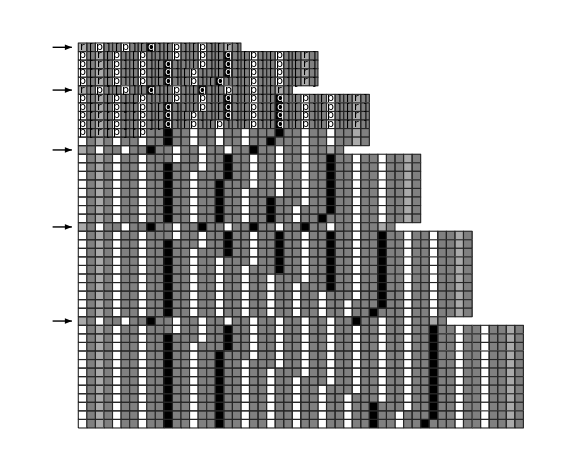

```mathematica
CAToSymb[rule_]:=Join[MapIndexed[With[{d=Fold[#1[#2]&,0[2],IntegerDigits[First[#2]-1,2,3]]},d->(d/.{0[2][y_]->0[x[#]]})]&,Reverse[IntegerDigits[rule,2,8]]],{r[x_]->p[r[p][p]][x],p[x_][p][p][r]->x[p][p][r]}]/.{0->p,1->q,2->x_};

With[{hist=Characters[ToString/@ResourceFunction["SymbolicSystem"][CAToSymb[90],r[p][p][q][p][p][r],44]]},Graphics[{MapIndexed[With[{gray=#1/.{"p"->1,"q"->0,"r"->2/3,_->1/2}},{EdgeForm[GrayLevel[.15]],GrayLevel[gray],Rectangle[{#2[[2]],-#2[[1]]}],If[gray<1/2,White,Black],Text[#1,{#2[[2]],-#2[[1]]+.06}+1/2]}]&,hist,{2}],Arrowheads[.02],Arrow[{{-2,#},{.25,#}}]&/@(.5-Flatten[Position[hist,{"r",__}]])},]]
```